# AntonAntonov/NumberTheoryUtilities

Number Theory utility functions

## Paclet Manifest

"Documentation"

"English"

"Guides"

"UtilitiesBreakdown.nb"DocumentationEnglishGuidesUtilitiesBreakdown.nb

"ReferencePages"

"Symbols"

"ChordTrailsPlot.nb"DocumentationEnglishReferencePagesSymbolsChordTrailsPlot.nb

"SpiralLattice.nb"DocumentationEnglishReferencePagesSymbolsSpiralLattice.nb

"SunflowerEmbedding.nb"DocumentationEnglishReferencePagesSymbolsSunflowerEmbedding.nb

"SunflowerEmbeddingPlot.nb"DocumentationEnglishReferencePagesSymbolsSunflowerEmbeddingPlot.nb

"TriangleMatrixEmbedding.nb"DocumentationEnglishReferencePagesSymbolsTriangleMatrixEmbedding.nb

"Tutorials"

"Kernel"

"NumberTheoryUtilities.wl"KernelNumberTheoryUtilities.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

Utility functions for visualizing Number theory relationships and phenomena.

### Details

The functions TriangleMatrixEmbedding and SpiralEmbedding give data structures for making Klauber triangles and Ulam spirals.

The function SunflowerEmbedding and SunflowerEmbeddingPlot are used to make sunflower embeddings data and visualizations.

SunflowerEmbedding can be given a function that classifies the positive integers into groups.

SunflowerEmbeddingPlot uses those groups to color the corresponding points.

ChordTrailsPlot and SunflowerEmbeddingPlot use all options of Graphics.

### Primary Context

AntonAntonov`NumberTheoryUtilities`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`NumberTheoryUtilities`"];
```

### Basic Examples

Make a Ulam's spiral embedding within a square with 11 rows and columns:

```mathematica
SpiralLattice[11]//Grid
```

101 | 100 | 99 | 98 | 97 | 96 | 95 | 94 | 93 | 92 | 91
102 | 65 | 64 | 63 | 62 | 61 | 60 | 59 | 58 | 57 | 90
103 | 66 | 37 | 36 | 35 | 34 | 33 | 32 | 31 | 56 | 89
104 | 67 | 38 | 17 | 16 | 15 | 14 | 13 | 30 | 55 | 88
105 | 68 | 39 | 18 | 5 | 4 | 3 | 12 | 29 | 54 | 87
106 | 69 | 40 | 19 | 6 | 1 | 2 | 11 | 28 | 53 | 86
107 | 70 | 41 | 20 | 7 | 8 | 9 | 10 | 27 | 52 | 85
108 | 71 | 42 | 21 | 22 | 23 | 24 | 25 | 26 | 51 | 84
109 | 72 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 83
110 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82
111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121

Make a triangular embedding of integers up to 10 triangle rows:

```mathematica
TriangleMatrixEmbedding[10, ""]//Grid
```

|  |  |  |  |  |  |  |  | 1 |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | 2 | 3 | 4 |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  | 5 | 6 | 7 | 8 | 9 |  |  |  |  |  |  | 
 |  |  |  |  |  | 10 | 11 | 12 | 13 | 14 | 15 | 16 |  |  |  |  |  | 
 |  |  |  |  | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 |  |  |  |  | 
 |  |  |  | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 |  |  |  | 
 |  |  | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 |  |  | 
 |  | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 |  | 
 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 
82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

Sunflower embedding of integers up to 2000 with primes shown in red:

```mathematica
SunflowerEmbeddingPlot[2000,PrimeQ,PlotStyle->{PointSize[0.016]},ColorFunction->(Blend[{GrayLevel[0.8],Red},#]&)]//Image
```

-Graphics-

### Scope

Show Klauber's triangle:

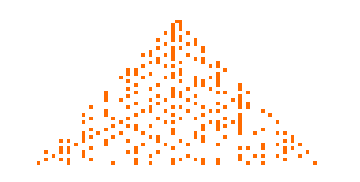

```mathematica
MatrixPlot[TriangleMatrixEmbedding[40]/.{(x_Integer/;!PrimeQ[x]):>0}//Unitize,ImageSize->Medium,Frame->False]
```

Show Ulam's spiral (finishing top-right):

```mathematica
s=SpiralLattice[21,"top-right"];
s2=s/.{(x_Integer/;!PrimeQ[x]):>"."}/.{(x_Integer):>Style[x,Red]};
Grid[s2]
```

421 | . | . | . | . | . | . | . | . | . | 431 | . | 433 | . | . | . | . | . | 439 | . | .
. | . | . | . | . | 347 | . | 349 | . | . | . | 353 | . | . | . | . | . | 359 | . | . | .
419 | . | . | . | . | . | 277 | . | . | . | 281 | . | 283 | . | . | . | . | . | . | . | .
. | . | . | 211 | . | . | . | . | . | . | . | . | . | . | . | 223 | . | . | . | . | .
. | . | 271 | . | 157 | . | . | . | . | . | 163 | . | . | . | 167 | . | . | . | 227 | . | .
. | . | . | . | . | . | . | 113 | . | . | . | . | . | . | . | . | . | . | . | 293 | .
. | . | 269 | . | . | . | 73 | . | . | . | . | . | 79 | . | . | . | . | . | 229 | . | 367
. | 337 | . | . | . | 109 | . | 43 | . | . | . | 47 | . | . | . | 83 | . | 173 | . | . | .
. | . | . | . | . | . | 71 | . | . | . | 23 | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | 107 | . | 41 | . | 7 | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | 151 | . | . | . | 19 | . | . | 2 | 11 | . | 53 | . | 127 | . | 233 | . | .
. | . | . | . | . | . | . | . | . | 5 | . | 3 | . | 29 | . | . | . | . | . | . | .
409 | . | 263 | . | 149 | . | 67 | . | 17 | . | . | . | 13 | . | . | . | . | . | . | . | 373
. | 331 | . | . | . | 103 | . | 37 | . | . | . | . | . | 31 | . | 89 | . | 179 | . | . | .
. | . | . | . | . | . | . | . | . | . | 61 | . | 59 | . | . | . | 131 | . | . | . | .
. | . | . | 199 | . | 101 | . | . | . | 97 | . | . | . | . | . | . | . | 181 | . | . | .
. | . | . | . | . | . | . | . | . | . | 139 | . | 137 | . | . | . | . | . | 239 | . | .
. | . | . | 197 | . | . | . | 193 | . | 191 | . | . | . | . | . | . | . | . | . | . | .
. | . | 257 | . | . | . | . | . | 251 | . | . | . | . | . | . | . | . | . | 241 | . | 379
. | . | . | . | . | . | . | . | . | 317 | . | . | . | 313 | . | 311 | . | . | . | 307 | .
401 | . | . | . | 397 | . | . | . | . | . | . | . | 389 | . | . | . | . | . | 383 | . | .

Show primitive root chord trails plot of 509 for its primitive root 75:

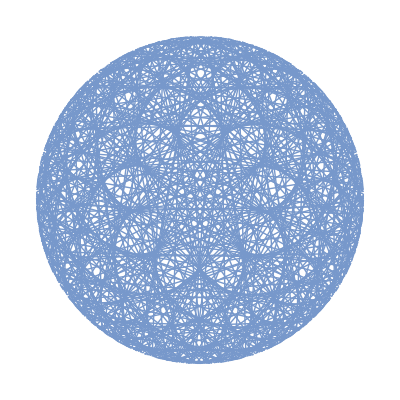

```mathematica
ChordTrailsPlot[509,75]
```

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-NumberTheoryUtilities-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Number theory

Ulam spiral

Triangular embedding

Spiral embedding

Sunflower embedding

Chords plot

Chord trails plot

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

UlamMatrix

SquareSpiralPoints

LatticePointsArrangement

### Original Source References and Attributions

GitHub - antononcube/Raku-Math-NumberTheory: Raku package with number theory functions.

### Links

Anton Antonov, "Primitive roots generation trails", (2025), Wolfram Community.

Number theory neat examples in Raku (Set 1) - YouTube

Number theory neat examples in Raku (Set 2) - YouTube

Number theory neat examples in Raku (Set 3) - YouTube

### Compatibility

#### Wolfram Language Version

14.3+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.